```mathematica
mnist=ResourceData["MNIST","TrainingData"];
```

```mathematica
group[i_]:=group[i]=Select[mnist,#[[2]]==i&][[All,1]];
nums={4,7,8};
data=Join@@group/@nums;
```

```mathematica
vec[img_]:=Flatten[ImageData[img]]
meanVec[set_]:=Total[vec/@set]/Length[set]
meanVecP[set_]:=Total[Parallelize[vec/@set]]/Length[set]
```

```mathematica
S[set_]:=Block[{mean=meanVec[set],mat=ConstantArray[0,{784,784}]},
Do[Block[{hey=vec[img]-mean},mat+=Outer[Times,hey,hey]],{img,set}];
mat/Length[set]
]
SP[set_]:=Block[{mean=meanVecP[set],mat},
ParallelEvaluate[mat=ConstantArray[0,{784,784}]];
ParallelDo[Block[{hey=vec[img]-mean},mat+=Outer[Times,hey,hey]],{img,set}];
Total[ParallelEvaluate[mat]]/Length[set]
]
```

```mathematica
Monitor[AbsoluteTiming[mat=S[data];],img]
AbsoluteTiming[matP=SP[data];]
Norm[Flatten[mat-matP]]
(*nums=Range[0,9];
data=Join@@group/@nums;
Monitor[AbsoluteTiming[mat=S[data];],img]
AbsoluteTiming[matP=SP[data];]*)
```

{10.3362,Null}

{10.841,Null}

1.0102×10^-12

```mathematica
pca[mat_,n_]:=Eigenvectors[mat,n]
```

```mathematica
eigs=Eigenvalues[matP];
runningTotal=Accumulate[eigs];
SelectFirst[runningTotal,#>=0.98runningTotal[[-1]]&->"Index"]
```

247

```mathematica
totalDistortion[A_,set_]:=Block[{mean=meanVec[set],proj=Transpose[A].A},Sum[Block[{hey=vec[img]-mean},Norm[proj.hey-hey]^2],{img,set}]]
totalDistortionP[A_,set_]:=Block[{mean=meanVecP[set],proj=Transpose[A].A},ParallelSum[Block[{hey=vec[img]-mean},Norm[proj.hey-hey]^2],{img,set}]]
```

```mathematica
dim=10;
A=pca[matP,dim];
AbsoluteTiming[totalDistortion[A,data]]
AbsoluteTiming[totalDistortionP[A,data]]
```

{0.397156,417057.}

{0.467983,417057.}

```mathematica
Table[totalDistortion[pca[mat,dim],data],{dim,{2,10,50,100,200,300}}]
```

{684924.,417057.,146378.,71555.5,26477.3,9846.02}

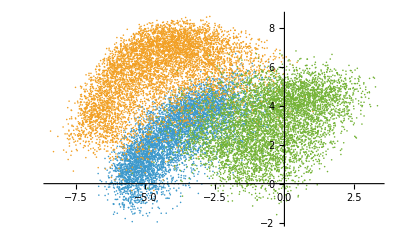

```mathematica
A2=pca[mat,2];
ListPlot[Transpose[A2.Transpose[vec/@group[#]]]&/@nums]
```

```mathematica
classMean[i_]:=classMean[i]=meanVec[group[i]]
cov[i_]:=cov[i]=SP[group[i]];
totalscatter=Sum[cov[i],{i,nums}];
betweenscatter=Block[{mean=meanVec[data]},Sum[Block[{hey=classMean[i]-mean},Length[group[i]]Outer[Times,hey,hey]],{i,nums}]];
ldaMat[λ_]:=Inverse[totalscatter+λ IdentityMatrix[784]].betweenscatter
```

```mathematica
lda[n_]:=Eigenvectors[ldaMat[10^-4],n]
```

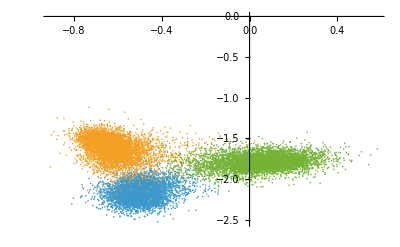

-Graphics3D-

```mathematica
B2=Chop[lda[2]];
ListPlot[Transpose[B2.Transpose[vec/@group[#]]]&/@nums,ImageSize->Full]
B3=Chop[lda[3]];
ListPointPlot3D[Transpose[B3.Transpose[vec/@group[#]]]&/@nums,ImageSize->Full]
```